# PHAS0012 Computing for Mathematical Physics

## Solutions 1: An Introduction to Computer Algebra

```mathematica
Clear["Global`*"]
```

## Some Elementary Mathematica Commands

### Simple Algebra

1.  Generate an expanded expression for the fifth power of (1 + 3x +  b y), and then try to recover a simpler form from the expansion. Use a new variable to save any expressions you might want to reuse.

```mathematica
ex=Expand[(1+3x+b y)^5]
Simplify[ex]
```

1+15 x+90 x^2+270 x^3+405 x^4+243 x^5+5 b y+60 b x y+270 b x^2 y+540 b x^3 y+405 b x^4 y+10 b^2 y^2+90 b^2 x y^2+270 b^2 x^2 y^2+270 b^2 x^3 y^2+10 b^3 y^3+60 b^3 x y^3+90 b^3 x^2 y^3+5 b^4 y^4+15 b^4 x y^4+b^5 y^5

(1+3 x+b y)^5

```mathematica
Factor[ex]
```

(1+3 x+b y)^5

Therefore, there are several ways to recover a simpler version. “Factor” factorises an expression, whereas “Simplify” will try a range of techniques including factorising.

2.  Extract the coefficient of x cubed from the expansion of the eighth power of (7x+8y).

```mathematica
Coefficient[(7x+8y)^8,x^3]
```

629407744 y^5

### Simple Calculus

3.  Find the integral with respect to x of 1/(5 x^2+1).

Note that the result is analytic, and square roots and other fractional powers are kept in that form rather than being converted to imprecise decimal numbers with a finite number of significant figures.

```mathematica
ii=Integrate[1/(5x^2+1),x]
```

ArcTan[√5 x]/(√5)

4.  Differentiation is also available: use it to check the result of the above integration. Try to get the result in a form that makes the check obvious.

```mathematica
D[ii,x]
```

1/(1+5 x^2)

5.  Find the derivative of x^(x^x)  (x to the x 
to the x, if  your  eyesight is failing!)

```mathematica
D[x^x^x,x]
```

x^(x^x) (x^(-1+x)+x^x Log[x] (1+Log[x]))

6.  Evaluate the definite integral ∫_0^∞ Sin[a z]^2/z^2 ⅆz.
Do this a) using pull-down symbols from the pallette; b) by writing the expression in Function notation.

```mathematica
∫_0^∞ Sin[a z]^2/z^2 ⅆz
Integrate[Sin[a z]^2/z^2,{z,0,Infinity}]
```

ConditionalExpression[1/2 π Abs[a],a∈ℝ]

ConditionalExpression[1/2 π Abs[a],a∈ℝ]

Comment

There's some useful maths here. Note that the condition that Mathematica returned means that it can only do the integral if a has no imaginary part. Let's see what would happen if a were complex,
            a = b + ⅈ c, 
 say. Then the sin term would be
          sin(a z) = (ⅇ^(ⅈ a z)- ⅇ^(- ⅈ a z))/(2 ⅈ) = (ⅇ^(ⅈ (b + ⅈ c) z)- ⅇ^(- ⅈ (b + ⅈ c) z))/(2 ⅈ)= (ⅇ^(ⅈ b z -  c z)- ⅇ^(- ⅈ b z +  c z))/(2 ⅈ)= (ⅇ^(ⅈ b z)ⅇ^(-  c z)- ⅇ^(- ⅈ b z)ⅇ^(c z))/(2 ⅈ)
   and we can see that if c is non-zero, whichever sign it has there is going to be a positive exponential term which goes to infinity as z goes to infinity, and the integral will diverge.

7.  Evaluate the integral of
		ⅇ^(-3 x-x^4)
	(a) as an indefinite integral
	(b) as a definite integral between 0 and ∞.  You will encounter functions in the answer that you have not met before: don't worry.

```mathematica
Integrate[Exp[-3x-x^4],x]
Integrate[Exp[-3x-x^4],{x,0,Infinity}]
```

∫ⅇ^(-3 x-x^4)ⅆx

1/8 (8 Gamma[5/4] HypergeometricPFQ[{},{1/2,3/4},81/256]-6 √π HypergeometricPFQ[{},{3/4,5/4},81/256]+9 Gamma[3/4] HypergeometricPFQ[{},{5/4,3/2},81/256]-9 HypergeometricPFQ[{1},{5/4,3/2,7/4},81/256])

Comment

There is an important point here: probably the majority of integrals that one can write down cannot be evaluated in closed form as indefinite integrals. However, a significant subset of these can be evaluated as definite integrals, usually between rather specific limits such as 0 and π, 0 and 1 or 0 and ∞.

### Algebraic Expressions, Expansions and Factorizations

8.  Use Mathematica to generate a series giving the terms up to the fifth power of x in the expansion of the square root of (1 + x) around x = 0, and check the first three terms in your calculation by deriving the Taylor series by hand. As a further check, evaluate the original square root, the series to five terms, and the series to three terms numerically for x=0.2.  You will need to use the function Normal[ ].

```mathematica
(* First, make sure x is clear of any value, so that it is used purely symbolically, then define the series to the 5th and 3rd terms with no terms giving "of the order of"*)

x=.
f5=Normal[Series[Sqrt[1+x],{x,0,5}]]
f3=Normal[Series[Sqrt[1+x],{x,0,3}]]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256

1+x/2-x^2/8+x^3/16

```mathematica
(* Then we define manually the first three coefficients of a Taylor series using the expression we want to expand*)

c1=Sqrt[1+x]
c2=(D[Sqrt[1+x],x])
c3=(1/2)(D[Sqrt[1+x],{x,2}])
```

√(1+x)

1/(2 √(1+x))

-1/(8 (1+x)^(3/2))

```mathematica
(* Now get the values of the function and its first and second derivatives at x=0 *)

x=0
c10=c1
c20=c2
c30=c3
```

0

1

1/2

-1/8

```mathematica
(* Next get the values of the series at x=0.2 *)

x=0.2
Sqrt[1+x]
f5
f3
c10+c20 x + c30 x^2
```

0.2

1.09545

1.09545

1.0955

1.095

```mathematica
(* Finally, clear x again *)
x=.
```

9.  Express (x-2)/(x^2 -1) in partial fractions.

```mathematica
Apart[(x-2)/(x^2-1)]
```

-1/(2 (-1+x))+3/(2 (1+x))

10. Express (x-2)/(1+x^2) in partial fractions. You will have to push Mathematica to do this, separating out the denominator and forcing it to be factorised into a form involving complex numbers.

```mathematica
Apart[(x-2)/(1+x^2)]
```

(-2+x)/(1+x^2)

```mathematica
Apart[(x-2)/Factor[(1+x^2)]]
```

(-2+x)/(1+x^2)

If there are complex coefficients, Factor can separate them out using Gaussian integer coefficients (Gaussian integer is a complex number whose real and imaginary parts are both integers):

```mathematica
Apart[(x-2)/Factor[(1+x^2), GaussianIntegers->True]]
```

(1/2+ⅈ)/(-ⅈ+x)+(1/2-ⅈ)/(ⅈ+x)

Alternatively, we can deal with the numerator and denominator separately and use the extension for Factor which allows the use of algebraic number fields (i.e. complex numbers):

```mathematica
pp=(x-2)/(1+x^2)
Apart[Numerator[pp]/Factor[Denominator[pp],Extension->I]]
```

(-2+x)/(1+x^2)

(1/2+ⅈ)/(-ⅈ+x)+(1/2-ⅈ)/(ⅈ+x)

11.  Evaluate the limit of the cotangent as its argument approaches π from below and from above.

```mathematica
Limit[Cot[θ],θ->π,Direction->+1]
Limit[Cot[θ],θ->π,Direction->-1]
Limit[Cot[θ],θ->π,Direction->"FromBelow"]
Limit[Cot[θ],θ->π,Direction->"FromAbove"]
```

-∞

∞

-∞

∞

Either format for specifying the direction is acceptable.

12.  Evaluate the limit as n tends to infinity of (1+p/n)^n.  Can you relate this to a well-known statistical distribution?

```mathematica
Limit[(1+p/n)^n,n->Infinity]
```

ⅇ^p

This is related to the fact that the binomial distribution tends to a Poisson as the number of trials becomes large and the probability of success in each trial becomes small.

13. Use Solve [] to find all the values of the sixth root of 1.

```mathematica
Solve[x^6==1,x]
```

{{x→-1},{x→1},{x→-(-1)^(1/3)},{x→(-1)^(1/3)},{x→-(-1)^(2/3)},{x→(-1)^(2/3)}}

14.  Solve the simultaneous equations
3 x+5 y+d z=13 a
19 x+e y+29 z=37 b
43 x+47 y+f z=61 c.

```mathematica
Solve[{3x+5y+d z==13a,
19x + e y + 29 z==37 b,
43 x + 47 y + f z==61 c},{x,y,z}]
```

{{x→-(-17719 a+8845 c+1739 b d-61 c d e-185 b f+13 a e f)/(-2146-893 d+43 d e+95 f-3 e f),y→-(16211 a-5307 c-1591 b d+1159 c d-247 a f+111 b f)/(-2146-893 d+43 d e+95 f-3 e f),z→-(11609 a+2738 b-5795 c-559 a e+183 c e)/(-2146-893 d+43 d e+95 f-3 e f)}}

15.  Solve the differential equation
Tan(x)+y'(x)=1.

```mathematica
DSolve[D[y[x],x]+Tan[x]==1,y[x],x]
```

{{y[x]→x+C[1]+Log[Cos[x]]}}

16. Solve the differential equation
y'(x)+y''(x)=1-Sin(x)
subject to the boundary conditions that y(0)=1/2 and y'(0)=3/2.

```mathematica
DSolve[{D[y[x],{x,2}]+D[y[x],x]==1-Sin[x],y[0]==1/2,y'[0]==3/2},y[x],x]
```

{{y[x]→1/2 (2 x+Cos[x]+Sin[x])}}

```mathematica
DSolve[{y'[x]+y''[x]==1-Sin[x],y[0]==1/2,y'[0]==3/2},y[x],x]
```

{{y[x]→1/2 (2 x+Cos[x]+Sin[x])}}

Comment

One of the commonest errors in this sort of problem is to forget, when setting the boundary conditions, that these have to be equations. That is, one might try something like

```mathematica
DSolve[{y'[x]+y''[x]==1-Sin[x],y[0]=1/2,y'[0]=3/2},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of 1/2 in the first argument {y'[x]+y''[x]==1-Sin[x],1/2,3/2}.

DSolve[{y'[x]+y''[x]==1-Sin[x],1/2,3/2},y[x],x]

This looks the way it does is because the result of a Set command such as lhs=rhs is the value of rhs. Now try to put things right

```mathematica
DSolve[{y'[x]+y''[x]==1-Sin[x],y[0]==1/2,y'[0]==3/2},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {y'[x]+y''[x]==1-Sin[x],True,True}.

DSolve[{y'[x]+y''[x]==1-Sin[x],True,True},y[x],x]

The problem here is that although we have put the boundary conditions in as equations, the values of y[0] and y'[0] are still there:

```mathematica
y[0]
y'[0]
```

1/2

3/2

so we have to clear those values first. If we don't, whenever we use y[0] the value set for it will be recalled, so that 
  y[0] == 1/2
is read as
  1/2==1/2
which is, of course, True. So what we need to do is

```mathematica
y[0]=.
y'[0]=.
DSolve[{y'[x]+y''[x]==1-Sin[x],y[0]==1/2,y'[0]==3/2},y[x],x]
```

{{y[x]→1/2 (2 x+Cos[x]+Sin[x])}}

17. Plot the graph of  (2 - θ^2) cos(4.25 π θ) as a function of θ for 0 ≤ θ ≤ 2.

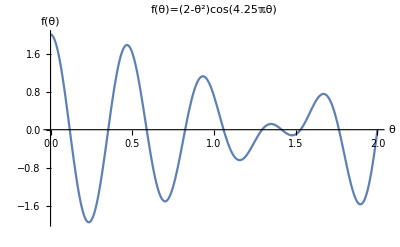

```mathematica
Plot[Cos[4.25θ π] (2-θ^2) ,{θ,0,2}, 
AxesLabel->{"θ", "f(θ)"}, 
PlotLabel->"f(θ)=(2-θ^2)cos(4.25ℼθ)"]
```

Finally, take some time to try a few problems of your own.

J. Bhamrah, A.H. Harker, J Underwood
UCL
December 2007, Revised January 2018, January 2020